```mathematica
<<Local`SrednickiInit`
```

Solve::tdep: The equations appear to involve the variables to be solved for in an essentially non-algebraic way.

Solve::eqf: λ_0 is not a well-formed equation.

Problem 28.1

```mathematica
PR[
"Following renormalization group procedure with(28.41):\n",
e2841=ℒ->-1/2 Subscript[Z, φ] guu[μ,α]xPartialD[φ,α]xPartialD[φ,μ]-1/2 Subscript[Z, m] m^2 φ^2-1/24 Subscript[Z, λ] λ (μ̃)^(ε/2)φ^4,
"\nand its bare field equation:",Yield,
b2841=ℒ->-1/2 guu[μ,α]xPartialD[Subscript[φ, 0],α]xPartialD[Subscript[φ, 0],μ]-1/2 Subscript[m, 0]^2 Subscript[φ, 0]^2-1/24 Subscript[λ, 0] Subscript[φ, 0]^4,
"\nWe determine the relationships:",Yield,
tmpr={Subscript[φ, 0]==√Subscript[Z, φ] φ,Subscript[m, 0]==√(Subscript[Z, m]/Subscript[Z, φ])m,Subscript[λ, 0]==(Subscript[Z, λ] λ (μ̃)^(ε/2))/Subscript[Z, φ]^2},
"\nWe use (28.9) for this case:",Yield,
e2809=Subscript[Z, λ]->1+HoldForm[Sum[(Subscript[c, n][α])/ε^n,{n,1,Infinity}]],
"  where:  ",tmpα=α->λ^2/(4 π)^2,
"\nFrom definition of λ_0:  ",
tmp=Map[#^2/(4 π)^2&,tmpr[[3]]]/.Reverse[tmpα],
"\nwe define: ",
tmpα0=Subscript[α, 0]->tmp[[2]],
"\nand ",tmpG[α_,ε_]->Log[Subscript[Z, λ]^2/Subscript[Z, φ]^4]
]
```

Following renormalization group procedure with(28.41):
ℒ→-1/2 m^2 φ^2 Z_m-1/24 λ φ^4 (μ̃)^(ε/2) Z_λ-1/2 Z_φ g_μα^μα xPartialD[φ,α] xPartialD[φ,μ]
and its bare field equation:
→ ℒ→-1/2 m_0^2 φ_0^2-1/24 λ_0 φ_0^4-1/2 g_μα^μα xPartialD[φ_0,α] xPartialD[φ_0,μ]
We determine the relationships:
→ {φ_0==φ √Z_φ,m_0==m √(Z_m/Z_φ),λ_0==(λ (μ̃)^(ε/2) Z_λ)/Z_φ^2}
We use (28.9) for this case:
→ Z_λ→1+∑_(n=1)^∞ c_n[α]/ε^n  where:  α→λ^2/(16 π^2)
From definition of λ_0:  λ_0^2/(16 π^2)==(α (μ̃)^ε Z_λ^2)/Z_φ^4
we define: α_0→(α (μ̃)^ε Z_λ^2)/Z_φ^4
and tmpG[α_,ε_]→Log[Z_λ^2/Z_φ^4]

λ^2 loop correction to propagator of ℒ_1⟶ φ^4.  The diagram:

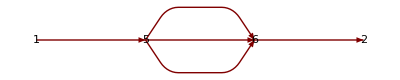

```mathematica
"λ^2 loop correction to propagator of ℒ_1⟶ φ^4.  The diagram: "
GraphPlot[{{1->5,k[1]},{5->6,q[1]},{5->6,q[2]},{5->6,q[3]},{6->2,k[2]}},VertexLabeling->True,DirectedEdges-> True,MultiedgeStyle->.5,VertexCoordinateRules->{1->{0,0},2->{3,0},5->{1,0},6->{2,0}} ]
```

```mathematica
"(14.04) to O[λ^2]"
e1404=Π[k_]->1/2(I λ)^2(-I)^2 IntegralOp[{{q[1]},{q[2]},{q[3]}},1/(2 π)^d Δ̃[q[1]]Δ̃[q[2]]Δ̃[q[3]]DiracDelta[k-q[1]-q[2]-q[3]]]-(A k^2+B m^2)
e1403=Δ̃[q_]->1/(q^2+m^2-I ϵ);
t1404=e1404/.e1403
"Use Feymann parameter trick."
sub=1/(A1_ A2_ A3_)-> IntegralOp[{{F[3]}},(x[1] A1+x[2] A2+x[3] A3)^-3];
sub=sub/.e1410;
tmp=t1404/.sub
"Which order of integration will be easier?"
tmp=tmp//.subIntInt2IntNoExpand;
tmp=tmp//IntegralOpMoveNVarOutAll;
tmpI=Extract[tmp,Position[tmp,IntegralOp[__]]][[1]]
tmpI=evalDeltaIntOver[tmpI,x[3]]/.ϵ->0 /.Last[xF[2]]->Last[Fn[2]](*remove ϵ for notational ease *)
```

(14.04) to O[λ^2]

Π[k_]→-A k^2-B m^2+1/2 λ^2 IntegralOp[{{q_1^1},{q_2^2},{q_3^3}},(2 π)^-d DiracDelta[k-q_1^1-q_2^2-q_3^3] Δ̃[q_1^1] Δ̃[q_2^2] Δ̃[q_3^3]]

Π[k_]→-A k^2-B m^2+1/2 λ^2 IntegralOp[{{q_1^1},{q_2^2},{q_3^3}},((2 π)^-d DiracDelta[k-q_1^1-q_2^2-q_3^3])/((m^2-ⅈ ϵ+(q_1^1)^2) (m^2-ⅈ ϵ+(q_2^2)^2) (m^2-ⅈ ϵ+(q_3^3)^2))]

Use Feymann parameter trick.

Π[k_]→-A k^2-B m^2+1/2 λ^2 IntegralOp[{{q_1^1},{q_2^2},{q_3^3}},(2 π)^-d DiracDelta[k-q_1^1-q_2^2-q_3^3] IntegralOp[{{x_1^1,0,1},{x_2^2,0,1},{x_3^3,0,1}},(2 DiracDelta[-1+x_1^1+x_2^2+x_3^3])/(((m^2-ⅈ ϵ+(q_1^1)^2) x_1^1+(m^2-ⅈ ϵ+(q_2^2)^2) x_2^2+(m^2-ⅈ ϵ+(q_3^3)^2) x_3^3)^3)]]

Which order of integration will be easier?

IntegralOp[{{q_1^1},{q_2^2},{q_3^3},{x_1^1,0,1},{x_2^2,0,1},{x_3^3,0,1}},(DiracDelta[k-q_1^1-q_2^2-q_3^3] DiracDelta[-1+x_1^1+x_2^2+x_3^3])/(((m^2-ⅈ ϵ+(q_1^1)^2) x_1^1+(m^2-ⅈ ϵ+(q_2^2)^2) x_2^2+(m^2-ⅈ ϵ+(q_3^3)^2) x_3^3)^3)]

IntegralOp[{{q_1^1},{q_2^2},{q_3^3},{x_1^1,0,1},{x_2^2,0,1-x_1^1}},DiracDelta[k-q_1^1-q_2^2-q_3^3]/(((m^2+(q_1^1)^2) x_1^1+(m^2+(q_3^3)^2) (1-x_1^1-x_2^2)+(m^2+(q_2^2)^2) x_2^2)^3)]

```mathematica
"Do x[2] integral"
tmp=tmpI;
"Simplify denominator"
tmpId=tmp[[2]]//Denominator//Simplify
tmpId=Collect[tmpId[[1]],{x[1],x[2]}];
tmpc=CoefficientList[tmpId,{x[2]}];
"Substitute A,B in integrand for simpler integration."
sub={A->tmpc[[1]],B->tmpc[[2]]}
tmp[[2]]=(tmp[[2]]//Numerator )/tmpId^3;
tmp0=tmp
"The x[2] integration is of form"
tmpi=1/(A+B x[2])^3
"and integrates to:"
tmp=IntegralOp[{Last[Fn[2]]},tmpi]/.subxIntegrateOne/.cleanInt;
irange=tmp[[2]];
tmp[[2]]=tmp[[2,1]];
tmp=tmp/.subIntegrate;
tmp=(tmp/.x[2]->irange[[3]])-(tmp/.x[2]->irange[[2]])
"substituting A,B"
tmp=tmp/.sub;
tmpI1=IntegralOp[tmp0[[1]]//Most,
(tmp0[[2]]//Numerator)tmp]
```

Do x[2] integral

Simplify denominator

(m^2+(q_1^1)^2 x_1^1+(q_2^2)^2 x_2^2-(q_3^3)^2 (-1+x_1^1+x_2^2))^3

Substitute A,B in integrand for simpler integration.

{A→m^2+(q_3^3)^2+((q_1^1)^2-(q_3^3)^2) x_1^1,B→(q_2^2)^2-(q_3^3)^2}

IntegralOp[{{q_1^1},{q_2^2},{q_3^3},{x_1^1,0,1},{x_2^2,0,1-x_1^1}},DiracDelta[k-q_1^1-q_2^2-q_3^3]/((m^2+(q_3^3)^2+((q_1^1)^2-(q_3^3)^2) x_1^1+((q_2^2)^2-(q_3^3)^2) x_2^2)^3)]

The x[2] integration is of form

1/((A+B x_2^2)^3)

and integrates to:

1/(2 A^2 B)-1/(2 B (A+B (1-x_1^1))^2)

substituting A,B

IntegralOp[{{q_1^1},{q_2^2},{q_3^3},{x_1^1,0,1}},DiracDelta[k-q_1^1-q_2^2-q_3^3] (1/(2 ((q_2^2)^2-(q_3^3)^2) (m^2+(q_3^3)^2+((q_1^1)^2-(q_3^3)^2) x_1^1)^2)-1/(2 ((q_2^2)^2-(q_3^3)^2) (m^2+(q_3^3)^2+((q_2^2)^2-(q_3^3)^2) (1-x_1^1)+((q_1^1)^2-(q_3^3)^2) x_1^1)^2))]

```mathematica
"2nd part of integral, x[1]"
tmpI2=tmpI1/.subxIntegrateOne/.subIntegralOp;
"Extract inner integral"
tmp2=tmpI2[[2]]/.distributeInt//IntegralOpMoveNVarOutAll;

posInt=Position[tmp2,IntegralOp[_,_]];
repl={};
For[iInt=1,iInt<=Length[posInt],iInt++,List[ pos=posInt[[iInt]]];
Int=Extract[tmp2,pos]//IntegralOpMoveNVarOutAll;
Print[Int,Yield,  (*simplify denominator*)
numer=Int[[2]]//Numerator;Yield;
denom=Int[[2]]//Denominator;Yield;
tmpc=CoefficientList[denom[[1]],{x[1]}];
sub={A->tmpc[[1]],B->tmpc[[2]]};
denom[[1]]=A+B x[1];Yield;
Int[[2]]=numer/denom;Yield;
tmp=Int/.subxIntegrateOne/.cleanInt;Yield;
irange=tmp[[2]];Yield;
tmp[[2]]=tmp[[2,1]];
tmp=tmp/.subIntegrate;Yield;
tmp=(tmp/.x[1]->irange[[3]])-(tmp/.x[1]->irange[[2]])//Simplify,Yield;
tmp=tmp/.sub;
AppendTo[repl,pos->tmp];""
];
];
tmpI2[[2]]=ReplacePart[tmp2,repl];
tmpI2
```

2nd part of integral, x[1]

Extract inner integral

IntegralOp[{{x_1^1,0,1}},1/((m^2+(q_3^3)^2+((q_1^1)^2-(q_3^3)^2) x_1^1)^2)]
→ 1/(A^2+A B)

IntegralOp[{{x_1^1,0,1}},1/((m^2+(q_3^3)^2+((q_2^2)^2-(q_3^3)^2) (1-x_1^1)+((q_1^1)^2-(q_3^3)^2) x_1^1)^2)]
→ 1/(A^2+A B)

IntegralOp[{{q_1^1},{q_2^2},{q_3^3}},-DiracDelta[k-q_1^1-q_2^2-q_3^3]/(2 (((q_1^1)^2-(q_2^2)^2) (m^2+(q_2^2)^2)+(m^2+(q_2^2)^2)^2) ((q_2^2)^2-(q_3^3)^2))+DiracDelta[k-q_1^1-q_2^2-q_3^3]/(2 ((q_2^2)^2-(q_3^3)^2) (((q_1^1)^2-(q_3^3)^2) (m^2+(q_3^3)^2)+(m^2+(q_3^3)^2)^2))]

```mathematica
tmp3=tmpI2/.distributeInt/.q[a_]^2->q[a].q[a];
tmp3=tmp3/.IntegralOp[a_,b_]:>evalDeltaIntOver[IntegralOp[a,b],q[3]];
tmp3=tmp3//IntegralOpMoveNVarOutAll
"Simplify denominators, external lines on shell."
repl={};
For[iInt=1,iInt<=Length[posInt],iInt++,List[ pos=posInt[[iInt]]];
Int=Extract[tmp3,pos]//IntegralOpMoveNVarOutAll;
Print[Int;Yield;
numer=Int[[2]]//Numerator;Yield;
denom=Int[[2]]//Denominator//Simplify;Yield;
denom=denom/.k.k->-m^2//.simpleDot;Yield;
denom=denom/.commuteDot//Simplify;Yield;
denom=denom/.Dot[q[a_],q[a_]]->q[a]^2//Simplify;Yield;
Int[[2]]=numer/denom;Yield,
Int,
"Can we complete the square on this?",Yield,
denom
(*
AppendTo[repl,pos->tmp];
*)
];
];
```

1/2 IntegralOp[{{q_1^1},{q_2^2}},1/(((-k.k-k.(-q_1^1)-k.(-q_2^2)-(-q_1^1).k-(-q_1^1).(-q_1^1)-(-q_1^1).(-q_2^2)+q_1^1.q_1^1-(-q_2^2).k-(-q_2^2).(-q_1^1)-(-q_2^2).(-q_2^2)) (m^2+k.k+k.(-q_1^1)+k.(-q_2^2)+(-q_1^1).k+(-q_1^1).(-q_1^1)+(-q_1^1).(-q_2^2)+(-q_2^2).k+(-q_2^2).(-q_1^1)+(-q_2^2).(-q_2^2))+(m^2+k.k+k.(-q_1^1)+k.(-q_2^2)+(-q_1^1).k+(-q_1^1).(-q_1^1)+(-q_1^1).(-q_2^2)+(-q_2^2).k+(-q_2^2).(-q_1^1)+(-q_2^2).(-q_2^2))^2) (-k.k-k.(-q_1^1)-k.(-q_2^2)-(-q_1^1).k-(-q_1^1).(-q_1^1)-(-q_1^1).(-q_2^2)-(-q_2^2).k-(-q_2^2).(-q_1^1)-(-q_2^2).(-q_2^2)+q_2^2.q_2^2))]-1/2 IntegralOp[{{q_1^1},{q_2^2}},1/((-k.k-k.(-q_1^1)-k.(-q_2^2)-(-q_1^1).k-(-q_1^1).(-q_1^1)-(-q_1^1).(-q_2^2)-(-q_2^2).k-(-q_2^2).(-q_1^1)-(-q_2^2).(-q_2^2)+q_2^2.q_2^2) ((q_1^1.q_1^1-q_2^2.q_2^2) (m^2+q_2^2.q_2^2)+(m^2+q_2^2.q_2^2)^2))]

Simplify denominators, external lines on shell.

→ IntegralOp[{{q_1^1},{q_2^2}},1/((m^2+2 k.q_1^1+2 k.q_2^2-2 q_1^1.q_2^2-(q_1^1)^2) (m^2+(q_1^1)^2) (-2 k.q_1^1-2 k.q_2^2+2 q_1^1.q_2^2+(q_1^1)^2+(q_2^2)^2))]Can we complete the square on this?
→ (m^2+2 k.q_1^1+2 k.q_2^2-2 q_1^1.q_2^2-(q_1^1)^2) (m^2+(q_1^1)^2) (-2 k.q_1^1-2 k.q_2^2+2 q_1^1.q_2^2+(q_1^1)^2+(q_2^2)^2)

→ IntegralOp[{{q_1^1},{q_2^2}},1/((m^2+2 k.q_1^1+2 k.q_2^2-2 q_1^1.q_2^2-(q_1^1)^2) (m^2+(q_1^1)^2) (m^2+(q_2^2)^2))]Can we complete the square on this?
→ (m^2+2 k.q_1^1+2 k.q_2^2-2 q_1^1.q_2^2-(q_1^1)^2) (m^2+(q_1^1)^2) (m^2+(q_2^2)^2)

```mathematica
sub=q[3]->k-q[1]-q[2]
q[3].q[3]/.sub//.simpleDot/.commuteDot/.Dot[k,k]->-m^2/.Dot[q[a_],q[a_]]->q[a]^2
```

q_3^3→k-q_1^1-q_2^2

-m^2-2 k.q_1^1-2 k.q_2^2+2 q_1^1.q_2^2+(q_1^1)^2+(q_2^2)^2